```mathematica
Ra=0.06;
Rv=0.016;
Rlv=1.2;
Ca=1.5;
Cv=50;
```

```mathematica
Elv[t_]:=(Sin[2 π t])^2+0.05
```

```mathematica
{pasol,pvsol,pvlsol} = NDSolveValue[{Ca pa'[t]==(plv[t]-pa[t])/Ra-(pa[t]-pv[t])/Rv,Cv pv'[t]==(pa[t]-pv[t])/Rv-(pv[t]-plv[t])/Rlv,(plv'[t]*Elv[t]-Elv'[t]*plv[t])/(Elv[t])^2==(pv[t]-plv[t])/Rlv-(plv[t]-pa[t])/Ra,pa[0]==0,plv[0]==0.85,pv[0]==0},{pa,pv,plv},{t,10}]
```

{InterpolatingFunction[{{0., 10.}}, <>],InterpolatingFunction[{{0., 10.}}, <>],InterpolatingFunction[{{0., 10.}}, <>]}

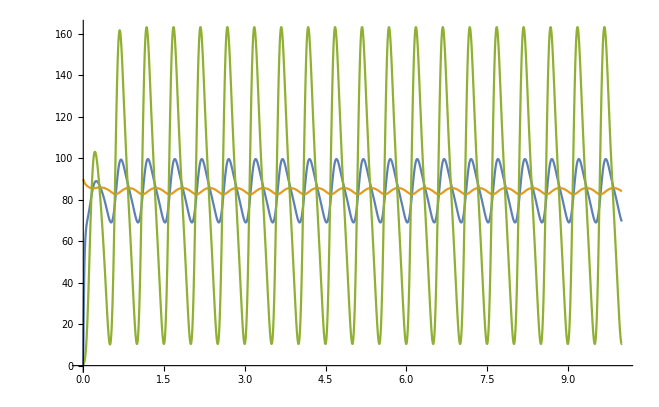

```mathematica
Plot[{pasol[x],pvsol[x],pvlsol[x]},{x,0,10}]
```

```mathematica
ClearAll[pv]
```